Group 16
Member Names: Ahmed Bilal(652836004), Shahzadi Agha(667263575), Chu-Chun Ku(673447297), Chen, Hsin-Chuan(658627471), Yi-Ting Lee(670706882) and Hsiang Lee(657783713)
Final Project for BDI 513

# -Graphics- Introduction

## In this project, we aim to analyse the top platforms for music releases and the top 15 songs. In addition, we want to get some type of idea of the genre and song type that is most recorded in our dataset. The purpose here is to highlight platforms that song producing companies should target to launch their music on. Along with this, the companies would get a hint of the types of sings popular among listeners on specific platforms and could redirect resources in producing more of these songs. Towards the end, we also highlight top 5 artists based on our data set which music companies could aim to hire for more successful songs. Persona: Our role is a business analyst at a record label. Our goal is to analyze interaction patterns across platforms, song performance, and cross-platform conversion efficiency to develop optimal promotional strategies for the company, enhancing the market impact of songs and the commercial value of artists. Problem Questions: 1) Which songs are most popular and on which music platform? 2) What kind/type of songs are popular on such platform? We focus on the following platforms: 1) Spotify 2) Tiktok 3) YouTube

## Initialization cell: Loading dataset and setting Notebook Directory

```mathematica
NotebookDirectory[]
SetDirectory[NotebookDirectory[]]
data=Import["Most Streamed Spotify Songs 20241.csv"];
```

/Users/ahmedbilal/Desktop/DS-Project/

/Users/ahmedbilal/Desktop/DS-Project

Filtering for 2024 records & data cleaning

```mathematica
(*Extract header and data separately*)
header=data[[1]];
data=data[[2;;]];  (*Remove the header*)

(*Ensure that the Release Date is properly parsed as DateObject and filter rows for 2024*)
data=Select[data[[2;;-1]],DateValue[#[[4]],"Year"]==2024&];

(*Remove rows with null values in the 8th,12th,and 16th columns*)
data=Select[data,NumberQ[#[[8]]]&];
data=Select[data,NumberQ[#[[12]]]&];
data=Select[data,NumberQ[#[[14]]]&];
data=Select[data,NumberQ[#[[16]]]&];

(*Add the header back to the filtered data*)
data=Prepend[data,header];
```

```mathematica
(*Extract relevant columns directly from the data*)
varSong = data[[2;;-1]][[All,1]];
varAlbum = data[[2;;-1]][[All,2]];
varArtist = data[[2;;-1]][[All,3]];
varReleaseDate = data[[2;;-1]][[All,4]];
varMonth=Table[DateObject[i,"Month"],{i,varReleaseDate}];
varYear=Table[DateObject[i,"Year"],{i,varReleaseDate}];
varKey = data[[2;;-1]][[All,5]];
varAllRank = data[[2;;-1]][[All,6]];
varTrackScore = data[[2;;-1]][[All,7]];
varSpotifyStreams = data[[2;;-1]][[All,8]];
varSpotifyPlaylistCount = data[[2;;-1]][[All,9]];
varSpotifyPlaylistReach = data[[2;;-1]][[All,10]];
varSpotifyPopularity = data[[2;;-1]][[All,11]];
varYoutubeViews = data[[2;;-1]][[All,12]];
varYoutubeLikes = data[[2;;-1]][[All,13]];
varYoutubePlaylistReach = data[[2;;-1]][[All,17]];
varTiktokPosts = data[[2;;-1]][[All,14]];
varTiktokLikes = data[[2;;-1]][[All,15]];
varTiktokViews = data[[2;;-1]][[All,16]];
```

## YouTube Engagement Analysis

### 1. Identify the top 15 songs based on YouTube (YT) views .

```mathematica
dataYoutubeViewsRank=ReverseSortBy[Transpose[{varYoutubeViews,varKey, varSong}],#[[1]]&];
dataYoutubeViewTop15=Take[dataYoutubeViewsRank,15];
```

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

### 2. Based on the top 15 songs by YT views, calculate the engagement rate using the formula Engagement Rate = YT Likes/YT Views

Definitions : 
- YouTube Views : Total views of the song' s official video on YouTube . 
- YouTube Likes : Total likes on the song' s official video on YouTube . 
Reason for Variable Selection : YouTube Views measure the song' s popularity, while YouTube Likes reflect the audience' s positive feedback . Together, these metrics provide a comprehensive measure of audience engagement and content popularity .

```mathematica
dataYoutubeViewsRank=ReverseSortBy[Transpose[{varSong,varYoutubeViews,varYoutubeLikes}],#[[2]]&];
dataYoutubeViewTop15=Take[dataYoutubeViewsRank,15];
YoutubeEngagementRateTop15=N[dataYoutubeViewTop15[[All,3]]/dataYoutubeViewTop15[[All,2]]]*100;  (*轉換為百分比*)

FinalTableYoutube=Transpose[Append[Transpose[dataYoutubeViewTop15],YoutubeEngagementRateTop15]];
```

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

### 3. Create a list

```mathematica
Grid[Prepend[MapIndexed[{#2[[1]],Short[#[[1]],10],#[[2]],#[[3]],Style[Row[{NumberForm[#[[4]],{4,2}],"%"}],Bold] }&,FinalTableYoutube],{"Rank","Song","YouTube Views","YouTube Likes","YouTube Engagement Rate"} ],Frame->All,Spacings->{2,1},Background->{{LightGray,None},{None,Lighter[Gray,0.9]}},Alignment->{{Center,Left,Center,Right}},ItemSize->{{2,10,15,8}},LabelStyle->Directive[Smaller]]
```

Rank | Song | YouTube Views | YouTube Likes | YouTube Engagement Rate
1 | SHEESH | 359896095 | 4907193 | 1.36%
2 | Gata Only | 228382568 | 1439495 | 0.63%
3 | Gulabi Sadi | 170115238 | 1923890 | 1.13%
4 | Stuck In The Middle | 147951356 | 1755973 | 1.19%
5 | Si No Quieres No | 135893150 | 889014 | 0.65%
6 | Smart | 130698280 | 1872592 | 1.43%
7 | i like the way you kiss me | 122599116 | 2228730 | 1.82%
8 | Not Like Us | 116347040 | 3486739 | 3.00%
9 | Supernova | 111310770 | 1724693 | 1.55%
10 | Espresso | 107550212 | 1825761 | 1.70%
11 | redrum | 105148629 | 1762297 | 1.68%
12 | Training Season | 66691067 | 961957 | 1.44%
13 | Casca de Bala | 63418833 | 427441 | 0.67%
14 | MASHA ULTRAFUNK | 57665106 | 1285063 | 2.23%
15 | HAY LUPITA | 51510163 | 439315 | 0.85%

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

### 4. Visualize the data with a bar chart

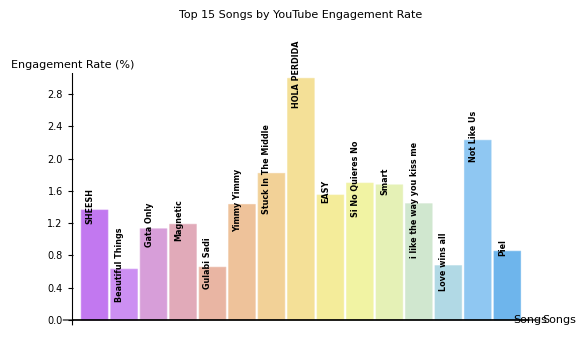

```mathematica
songNames={"SHEESH","Beautiful Things","Gata Only","Magnetic","Gulabi Sadi","Yimmy Yimmy","Stuck In The Middle","HOLA PERDIDA","EASY","Si No Quieres No","Smart","i like the way you kiss me","Love wins all","Not Like Us","Piel"};

rotateLabels[labels_]:=Placed[Style[#,Italic,FontSize->8,Black]&/@labels,Above,Rotate[#,90 Degree]&];

youTubeChart=BarChart[YoutubeEngagementRateTop15,ChartLabels->rotateLabels[songNames],ChartStyle->"Pastel",ImageSize->Large,LabelStyle->Directive[Bold,Black,Medium],PlotLabel->"Top 15 Songs by YouTube Engagement Rate",AxesLabel->{"Songs","Engagement Rate (%)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]
```

### Analysis - YouTube Engagement Rates

YouTube shows the lowest Engagement Rates, with values from 0.4 % to 16 % . This suggests that while YouTube is still a major platform for discovering music, users tend to watch passively instead of engaging actively with likes or comments . People often just click on a video to watch, without necessarily interacting much, which results in lower engagement .

## TikTok Engagement Analysis

### 1. Identify the top 15 songs based on TikTok posts

```mathematica
dataTikTokPostsRank=ReverseSortBy[Transpose[{varTiktokPosts,varKey, varSong}],#[[1]]&];
dataTikTokPostsTop15=Take[dataTikTokPostsRank,15];
```

### 2. Based on the top 15 songs by TikTok posts, calculate the engagement rate using the formula Engagement Rate = TikTok Posts/TikTok Views

Definitions : 
- TikTok Views : Total views on TikTok posts featuring the song . 
- TikTok Posts : Number of TikTok posts featuring the song . 
Reason for Selection : 
(1) TikTok Views reflect the reach of the song' s content, while TikTok Posts indicate user creativity and engagement . Together, these metrics provide a comprehensive measure of user interaction with the song . 
(2) A high Posts/Views ratio suggests users are willing to actively create content, indicating the song' s potential for viral growth . 
(3) A high Engagement Rate (Posts) shows that users not only enjoy the song but are also inspired to use it in their content creation .

```mathematica
dataTikTokPostsRank=ReverseSortBy[Transpose[{varSong,varTiktokPosts,varTiktokViews}],#[[2]]&];
dataTikTokPostsTop15=Take[dataTikTokPostsRank,15];

TikTokEngagementRateTop15=N[dataTikTokPostsTop15[[All,2]]/dataTikTokPostsTop15[[All,3]]]*100;

FinalTableTikTok=Transpose[Append[Transpose[dataTikTokPostsTop15],TikTokEngagementRateTop15]];
```

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

### 3. Create a list

```mathematica
Grid[Prepend[MapIndexed[{#2[[1]],Short[#[[1]],10],#[[2]],#[[3]],Style[Row[{NumberForm[#[[4]],{4,2}],"%"}],Bold] }&,FinalTableTikTok],{"Rank","Song","TikTok Posts","TikTok Views","TikTok Engagement Rate"} ],Frame->All,Spacings->{2,1},Background->{{LightGray,None},{None,Lighter[Gray,0.9]}},Alignment->{{Center,Left,Center,Right}},ItemSize->{{2,10,15,8}},LabelStyle->Directive[Smaller]]
```

Rank | Song | TikTok Posts | TikTok Views | TikTok Engagement Rate
1 | Gata Only | 3500000 | 3804584163 | 0.09%
2 | i like the way you kiss me | 3025400 | 3369120610 | 0.09%
3 | Casca de Bala | 1600000 | 8850449 | 18.08%
4 | Montagem Rave Eterno | 1100000 | 3900000 | 28.21%
5 | BLUE | 941900 | 1225345800 | 0.08%
6 | No Se Vale | 871174 | 441343495 | 0.20%
7 | Not Like Us | 674700 | 208339025 | 0.32%
8 | MASHA ULTRAFUNK | 550000 | 1059880600 | 0.05%
9 | Nasty | 535464 | 1051026401 | 0.05%
10 | Asylum | 426600 | 67702628 | 0.63%
11 | Get It Sexyy | 361700 | 476545000 | 0.08%
12 | BIRDS OF A FEATHER | 251200 | 443104700 | 0.06%
13 | SHEESH | 212500 | 390081328 | 0.05%
14 | Espresso | 209200 | 1379499000 | 0.02%
15 | PLIS | 202354 | 336367149 | 0.06%

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

### 4. Visualize the data with a bar chart

Use a logarithmic scale to address the issue of a wide data range, ensuring differences in engagement rates are not overly exaggerated and improving visual clarity .

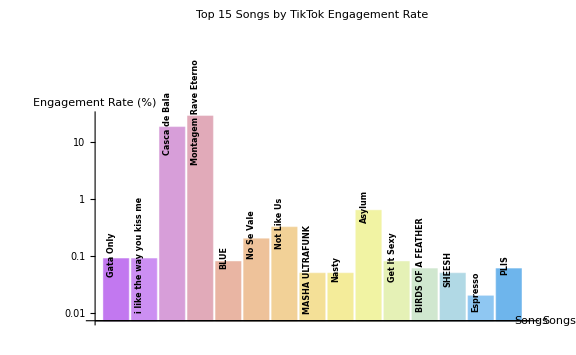

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

```mathematica
TikTokEngagementRateTop15={0.09,0.09,18.08,28.21,0.08,0.20,0.32,0.05,0.05,0.63,0.08,0.06,0.05,0.02,0.06};

songNames={"Gata Only","i like the way you kiss me","Casca de Bala","Montagem Rave Eterno","BLUE","No Se Vale","Not Like Us","MASHA ULTRAFUNK","Nasty","Asylum","Get It Sexy","BIRDS OF A FEATHER","SHEESH","Espresso","PLIS"};
rotateLabels[labels_]:=Placed[Style[#,Italic,FontSize->8,Black]&/@labels,Above,Rotate[#,90 Degree]&];
tikTokChart=BarChart[TikTokEngagementRateTop15,ChartLabels->rotateLabels[songNames],ChartStyle->"Pastel",ImageSize->Large,LabelStyle->Directive[Bold,Black,Medium],PlotLabel->"Top 15 Songs by TikTok Engagement Rate",AxesLabel->{"Songs","Engagement Rate (%)"},ScalingFunctions->"Log",(*對數縮放*)BaseStyle->{FontFamily->"Arial",FontSize->12}]
```

### Analysis - TikTok Engagement Rates

TikTok' s Engagement Rates vary significantly, ranging from 0.02 % to 28.21 % . While many songs show lower engagement rates, this reflects TikTok' s unique nature as a platform for quick, viral content . Even with lower percentages, users are engaging with songs in short video formats, highlighting the platform' s ability to enhance a song' s visibility and viral spread . The data indicates that songs with higher engagement rates, such as "Montagem Rave Eterno" (28.21 %), benefit from active user creativity, driving significant interaction and viral potential .

## Spotify Engagement Analysis and Cross-Platform Comparison

### 1. Identify the top 15 songs based on Spotify streams

```mathematica
dataSpotifyStreamsRank=ReverseSortBy[Transpose[{varSpotifyStreams,varKey, varSong}],#[[1]]&];
dataSpotifyStreamsTop15=Take[dataSpotifyStreamsRank,15];
```

### 2. Based on the top 15 songs by Spotify streams, calculate the engagement rate using the formula Engagement Rate = Spotify Streams/Spotify Playlist Reach

Definitions : 
- Spotify Streams : Total number of streams on Spotify . 
- Spotify Playlist Reach : Reach of the song across Spotify playlists . 
Reason for Selection : Using Spotify Streams and Spotify Playlist Reach to calculate the engagement rate helps measure how many listeners in a playlist audience actually stream the song, providing an indication of the song' s popularity .

```mathematica
dataSpotifyStreamsRank=ReverseSortBy[Transpose[{varSong,varSpotifyStreams,varSpotifyPlaylistReach}],#[[2]]&];
dataSpotifyStreamsTop15=Take[dataSpotifyStreamsRank,15];

SpotifyEngagementRateTop15=N[dataSpotifyStreamsTop15[[All,2]]/dataSpotifyStreamsTop15[[All,3]]]*100;  

FinalTableSpotify=Transpose[Append[Transpose[dataSpotifyStreamsTop15],SpotifyEngagementRateTop15]];
```

### 3. Create a list

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

```mathematica
Grid[Prepend[MapIndexed[{#2[[1]],Short[#[[1]],10],#[[2]],#[[3]],Style[Row[{NumberForm[#[[4]],{4,2}],"%"}],Bold] }&,FinalTableSpotify],{"Rank","Song","Spotify Streams","Spotify Playlist Reach","Spotify Engagement Rate"} ],Frame->All,Spacings->{2,1},Background->{{LightGray,None},{None,Lighter[Gray,0.9]}},Alignment->{{Center,Left,Center,Right}},ItemSize->{{2,10,15,8}},LabelStyle->Directive[Smaller]]
```

Rank | Song | Spotify Streams | Spotify Playlist Reach | Spotify Engagement Rate
1 | Gata Only | 675079153 | 211236940 | 319.60%
2 | i like the way you kiss me | 601309283 | 211607669 | 284.20%
3 | Espresso | 547882871 | 262343414 | 208.80%
4 | redrum | 428233003 | 144298748 | 296.80%
5 | Not Like Us | 323703884 | 174597137 | 185.40%
6 | Training Season | 251153869 | 92985554 | 270.10%
7 | I Can Do It With a Broken Heart | 250430303 | 134357870 | 186.40%
8 | LUNCH | 221636195 | 197280692 | 112.30%
9 | BIRDS OF A FEATHER | 214237645 | 202626837 | 105.70%
10 | Down Bad | 210385853 | 38317286 | 549.10%
11 | Whatever She Wants | 207093873 | 114051028 | 181.60%
12 | the boy is mine | 175336290 | 79812251 | 219.70%
13 | Smart | 159256689 | 20291074 | 784.90%
14 | Si No Quieres No | 158131138 | 71590238 | 220.90%
15 | SHEESH | 124893397 | 25936342 | 481.50%

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

### 4. Visualize the data with a bar chart

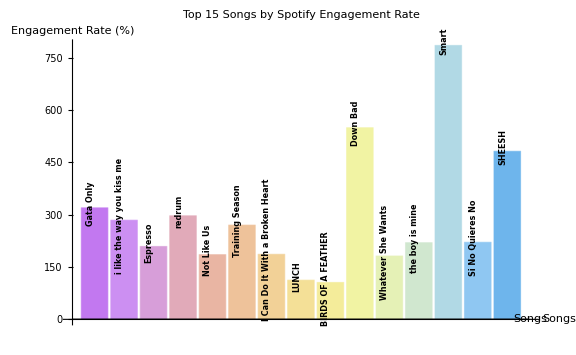

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

```mathematica
songNames={"Gata Only","i like the way you kiss me","Espresso","redrum","Not Like Us","Training Season","I Can Do It With a Broken Heart","LUNCH","BIRDS OF A FEATHER","Down Bad","Whatever She Wants","the boy is mine","Smart","Si No Quieres No","SHEESH"};

rotateLabels[labels_]:=Placed[Style[#,Italic,FontSize->8,Black]&/@labels,Above,Rotate[#,90 Degree]&];

spotifyChart=BarChart[SpotifyEngagementRateTop15,ChartLabels->rotateLabels[songNames],ChartStyle->"Pastel",ImageSize->Large,LabelStyle->Directive[Bold,Black,Medium],PlotLabel->"Top 15 Songs by Spotify Engagement Rate",AxesLabel->{"Songs","Engagement Rate (%)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]
```

### Analysis - Spotify Engagement Rates

The Engagement Rates on Spotify range from 105 % to 549 % . This is a pretty strong level of engagement, meaning that users on Spotify are paying close attention to the songs . It shows that people are more likely to listen to these tracks multiple times, which indicates strong user interest and loyalty .

### Insights and Cross Platform Comparisons

YouTube' s Passive Listening : 
The low engagement on YouTube points to the fact that users are often just watching music videos without interacting much . This is typical for a platform where the focus is on video content rather than direct engagement with the song itself .
       
TikTok' s Viral Impact : 
While TikTok' s engagement is lower, the platform' s nature means that even a short burst of attention can make a big impact . Users might not engage deeply, but TikTok' s focus on viral content means that a song can quickly gain popularity and reach a wide audience .
    
Spotify' s High Engagement :
The higher Engagement Rates on Spotify suggest that users are more invested in the music, often listening to it over and over . This is a good sign of long - term interest and shows that Spotify is great at building a strong connection between users and songs .

#### Conclusion

When comparing the three platforms, Spotify shows the highest engagement, indicating that users are more likely to listen to songs repeatedly, suggesting strong user interest and long - term loyalty . TikTok, while showing lower engagement, proves to be a powerful platform for generating viral visibility, where quick bursts of interaction can make a song popular rapidly . YouTube, on the other hand, shows the lowest engagement, with users primarily consuming music passively through video views rather than actively engaging with the content . These differences highlight the unique roles each platform plays in music consumption, with Spotify fostering deeper connections, TikTok driving viral trends, and YouTube focusing on passive listening . Understanding these patterns can help artists and marketers tailor their strategies to each platform' s strengths .

## Conversion Rate Analysis

### Youtube Views ⟺ Spotify Streams Conversion Rate Analysis

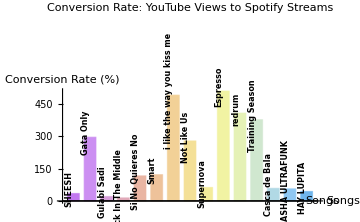
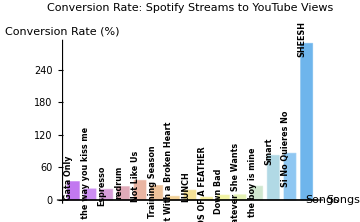
{Rank | Song Name | YouTube Views | Spotify Streams | Conversion Rate (Spotify/YouTube)
1 | SHEESH | 359,896,095 | 124,893,397 | 34.70%
2 | Gata Only | 228,382,568 | 675,079,153 | 295.60%
3 | Gulabi Sadi | 170,115,238 | 34,996,527 | 20.57%
4 | Stuck In The Middle | 147,951,356 | 21,167,612 | 14.31%
5 | Si No Quieres No | 135,893,150 | 158,131,138 | 116.40%
6 | Smart | 130,698,280 | 159,256,689 | 121.90%
7 | i like the way you kiss me | 122,599,116 | 601,309,283 | 490.50%
8 | Not Like Us | 116,347,040 | 323,703,884 | 278.20%
9 | Supernova | 111,310,770 | 69,729,033 | 62.64%
10 | Espresso | 107,550,212 | 547,882,871 | 509.40%
11 | redrum | 105,148,629 | 428,233,003 | 407.30%
12 | Training Season | 66,691,067 | 251,153,869 | 376.60%
13 | Casca de Bala | 63,418,833 | 37,157,630 | 58.59%
14 | MASHA ULTRAFUNK | 57,665,106 | 32,435,333 | 56.25%
15 | HAY LUPITA | 51,510,163 | 22,692,011 | 44.05%,-Graphics-,Rank | Song Name | Spotify Streams | YouTube Views | Conversion Rate (YouTube/Spotify)
1 | Gata Only | 675,079,153 | 228,382,568 | 33.83%
2 | i like the way you kiss me | 601,309,283 | 122,599,116 | 20.39%
3 | Espresso | 547,882,871 | 107,550,212 | 19.63%
4 | redrum | 428,233,003 | 105,148,629 | 24.55%
5 | Not Like Us | 323,703,884 | 116,347,040 | 35.94%
6 | Training Season | 251,153,869 | 66,691,067 | 26.55%
7 | I Can Do It With a Broken Heart | 250,430,303 | 16,747,466 | 6.69%
8 | LUNCH | 221,636,195 | 40,022,524 | 18.06%
9 | BIRDS OF A FEATHER | 214,237,645 | 11,033,725 | 5.15%
10 | Down Bad | 210,385,853 | 18,713,330 | 8.89%
11 | Whatever She Wants | 207,093,873 | 19,787,472 | 9.55%
12 | the boy is mine | 175,336,290 | 44,458,370 | 25.36%
13 | Smart | 159,256,689 | 130,698,280 | 82.07%
14 | Si No Quieres No | 158,131,138 | 135,893,150 | 85.94%
15 | SHEESH | 124,893,397 | 359,896,095 | 288.20%,-Graphics-}

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

```mathematica
youtubeToSpotifyData=ReverseSortBy[Transpose[{varSong,varYoutubeViews,varSpotifyStreams}],#[[2]]&];
youtubeToSpotifyTop15=Take[youtubeToSpotifyData,15];

spotifyToYoutubeData=ReverseSortBy[Transpose[{varSong,varSpotifyStreams,varYoutubeViews}],#[[2]]&];
spotifyToYoutubeTop15=Take[spotifyToYoutubeData,15];

youtubeToSpotifyConversion=N[youtubeToSpotifyTop15[[All,3]]/youtubeToSpotifyTop15[[All,2]]]*100;

spotifyToYoutubeConversion=N[spotifyToYoutubeTop15[[All,3]]/spotifyToYoutubeTop15[[All,2]]]*100;
youtubeToSpotifyTable=Map[{#[[1]],#[[2]],#[[3]],#[[4]]}&,Transpose[{youtubeToSpotifyTop15[[All,1]],youtubeToSpotifyTop15[[All,2]],youtubeToSpotifyTop15[[All,3]],youtubeToSpotifyConversion}]];


spotifyToYoutubeTable=Map[{#[[1]],#[[2]],#[[3]],#[[4]]}&,Transpose[{spotifyToYoutubeTop15[[All,1]],spotifyToYoutubeTop15[[All,2]],spotifyToYoutubeTop15[[All,3]],spotifyToYoutubeConversion}]];
youtubeToSpotifyGrid=Grid[Prepend[MapIndexed[{#2[[1]],#[[1]],Style[NumberForm[#[[2]],DigitBlock->3],Bold,14],Style[NumberForm[#[[3]],DigitBlock->3],Bold,14],Style[Row[{NumberForm[#[[4]],{4,2}],"%"}],Bold,14]}&,youtubeToSpotifyTable],{"Rank","Song Name","YouTube Views","Spotify Streams","Conversion Rate (Spotify/YouTube)"}],Frame->All,Spacings->{2,1},Background->{{LightGray,None},{None,LighterGray[0.9]}},Alignment->{{Center,Left,Center,Right,Right}},ItemSize->{{2,15,20,15,10}},LabelStyle->Directive[Bold,16]];

spotifyToYoutubeGrid=Grid[Prepend[MapIndexed[{#2[[1]],#[[1]],Style[NumberForm[#[[2]],DigitBlock->3],Bold,14],Style[NumberForm[#[[3]],DigitBlock->3],Bold,14],Style[Row[{NumberForm[#[[4]],{4,2}],"%"}],Bold,14]}&,spotifyToYoutubeTable],{"Rank","Song Name","Spotify Streams","YouTube Views","Conversion Rate (YouTube/Spotify)"}],Frame->All,Spacings->{2,1},Background->{{LightGray,None},{None,LighterGray[0.9]}},Alignment->{{Center,Left,Center,Right,Right}},ItemSize->{{2,15,20,15,10}},LabelStyle->Directive[Bold,16]];

yTtoSpisongNames={"SHEESH","Gata Only","Gulabi Sadi","Stuck In The Middle","Si No Quieres No","Smart","i like the way you kiss me","Not Like Us","Supernova","Espresso","redrum","Training Season","Casca de Bala","MASHA ULTRAFUNK","HAY LUPITA"};

rotateLabels[labels_]:=Placed[Style[#,Italic,FontSize->8,Black]&/@labels,Above,Rotate[#,90 Degree]&];


youtubeToSpotifyBarChart=BarChart[youtubeToSpotifyConversion,ChartLabels->rotateLabels[yTtoSpisongNames],ChartStyle->"Pastel",PlotLabel->"Conversion Rate: YouTube Views to Spotify Streams",LabelStyle->Directive[Bold,Black,Smaller],AxesLabel->{"Songs","Conversion Rate (%)"},ImageSize->Medium,BarSpacing->0.4,ScalingFunctions->None];

spotifyToYoutubesongNames={"Gata Only","i like the way you kiss me","Espresso","redrum","Not Like Us","Training Season","I Can Do It With a Broken Heart","LUNCH","BIRDS OF A FEATHER","Down Bad","Whatever She Wants","the boy is mine","Smart","Si No Quieres No","SHEESH"};

spotifyToYoutubeBarChart=BarChart[spotifyToYoutubeConversion,ChartLabels->rotateLabels[spotifyToYoutubesongNames],ChartStyle->"Pastel",PlotLabel->"Conversion Rate: Spotify Streams to YouTube Views",LabelStyle->Directive[Bold,Black,Smaller],AxesLabel->{"Songs","Conversion Rate (%)"},ImageSize->Medium,BarSpacing->0.4,ScalingFunctions->None];

{youtubeToSpotifyGrid,youtubeToSpotifyBarChart,spotifyToYoutubeGrid,spotifyToYoutubeBarChart}
```

### TikTok Views ⟺ Spotify Streams Conversion Rate Analysis

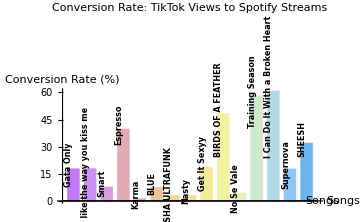
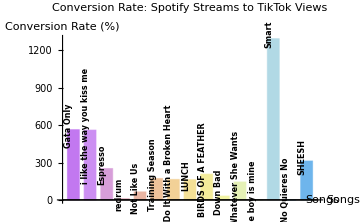
{Rank | Song Name | TikTok Views | Spotify Streams | Conversion Rate (Spotify/TikTok)
1 | Gata Only | 3,804,584,163 | 675,079,153 | 17.74%
2 | i like the way you kiss me | 3,369,120,610 | 601,309,283 | 17.85%
3 | Smart | 2,059,824,051 | 159,256,689 | 7.73%
4 | Espresso | 1,379,499,000 | 547,882,871 | 39.72%
5 | Karma | 1,314,113,353 | 17,310,258 | 1.32%
6 | BLUE | 1,225,345,800 | 91,272,461 | 7.45%
7 | MASHA ULTRAFUNK | 1,059,880,600 | 32,435,333 | 3.06%
8 | Nasty | 1,051,026,401 | 31,612,906 | 3.01%
9 | Get It Sexyy | 476,545,000 | 89,362,910 | 18.75%
10 | BIRDS OF A FEATHER | 443,104,700 | 214,237,645 | 48.35%
11 | No Se Vale | 441,343,495 | 19,388,370 | 4.39%
12 | Training Season | 431,390,500 | 251,153,869 | 58.22%
13 | I Can Do It With a Broken Heart | 411,722,900 | 250,430,303 | 60.82%
14 | Supernova | 393,973,528 | 69,729,033 | 17.70%
15 | SHEESH | 390,081,328 | 124,893,397 | 32.02%,-Graphics-,Rank | Song Name | Spotify Streams | TikTok Views | Conversion Rate (TikTok/Spotify)
1 | Gata Only | 675,079,153 | 3,804,584,163 | 563.60%
2 | i like the way you kiss me | 601,309,283 | 3,369,120,610 | 560.30%
3 | Espresso | 547,882,871 | 1,379,499,000 | 251.80%
4 | redrum | 428,233,003 | 43,993,800 | 10.27%
5 | Not Like Us | 323,703,884 | 208,339,025 | 64.36%
6 | Training Season | 251,153,869 | 431,390,500 | 171.80%
7 | I Can Do It With a Broken Heart | 250,430,303 | 411,722,900 | 164.40%
8 | LUNCH | 221,636,195 | 360,017,000 | 162.40%
9 | BIRDS OF A FEATHER | 214,237,645 | 443,104,700 | 206.80%
10 | Down Bad | 210,385,853 | 65,541,536 | 31.15%
11 | Whatever She Wants | 207,093,873 | 298,300,000 | 144.00%
12 | the boy is mine | 175,336,290 | 3,842,071 | 2.19%
13 | Smart | 159,256,689 | 2,059,824,051 | 1293.00%
14 | Si No Quieres No | 158,131,138 | 147,200 | 0.09%
15 | SHEESH | 124,893,397 | 390,081,328 | 312.30%,-Graphics-}

Wolfram`Chatbook`Chatbook::Internal: An unexpected error occurred. Report this issue »

```mathematica
tiktokToSpotifyData=ReverseSortBy[Transpose[{varSong,varTiktokViews,varSpotifyStreams}],#[[2]]&];
tiktokToSpotifyTop15=Take[tiktokToSpotifyData,15];

spotifyToTiktokData=ReverseSortBy[Transpose[{varSong,varSpotifyStreams,varTiktokViews}],#[[2]]&];
spotifyToTiktokTop15=Take[spotifyToTiktokData,15];

tiktokToSpotifyConversion=N[tiktokToSpotifyTop15[[All,3]]/tiktokToSpotifyTop15[[All,2]]]*100;

spotifyToTiktokConversion=N[spotifyToTiktokTop15[[All,3]]/spotifyToTiktokTop15[[All,2]]]*100;

tiktokToSpotifyTable=Map[{#[[1]],#[[2]],#[[3]],#[[4]]}&,Transpose[{tiktokToSpotifyTop15[[All,1]],tiktokToSpotifyTop15[[All,2]],tiktokToSpotifyTop15[[All,3]],tiktokToSpotifyConversion}]];

spotifyToTiktokTable=Map[{#[[1]],#[[2]],#[[3]],#[[4]]}&,Transpose[{spotifyToTiktokTop15[[All,1]],spotifyToTiktokTop15[[All,2]],spotifyToTiktokTop15[[All,3]],spotifyToTiktokConversion}]];

tiktokToSpotifyGrid=Grid[Prepend[MapIndexed[{#2[[1]],#[[1]],Style[NumberForm[#[[2]],DigitBlock->3],Bold,14],Style[NumberForm[#[[3]],DigitBlock->3],Bold,14],Style[Row[{NumberForm[#[[4]],{4,2}],"%"}],Bold,14]}&,tiktokToSpotifyTable],{"Rank","Song Name","TikTok Views","Spotify Streams","Conversion Rate (Spotify/TikTok)"}],Frame->All,Spacings->{2,1},Background->{{LightGray,None},{None,LighterGray[0.9]}},Alignment->{{Center,Left,Center,Right,Right}},ItemSize->{{2,15,20,15,10}},LabelStyle->Directive[Bold,16]];

spotifyToTiktokGrid=Grid[Prepend[MapIndexed[{#2[[1]],#[[1]],Style[NumberForm[#[[2]],DigitBlock->3],Bold,14],Style[NumberForm[#[[3]],DigitBlock->3],Bold,14],Style[Row[{NumberForm[#[[4]],{4,2}],"%"}],Bold,14]}&,spotifyToTiktokTable],{"Rank","Song Name","Spotify Streams","TikTok Views","Conversion Rate (TikTok/Spotify)"}],Frame->All,Spacings->{2,1},Background->{{LightGray,None},{None,LighterGray[0.9]}},Alignment->{{Center,Left,Center,Right,Right}},ItemSize->{{2,15,20,15,10}},LabelStyle->Directive[Bold,16]];

tikToktoSpotifysongNames={"Gata Only","i like the way you kiss me","Smart","Espresso","Karma","BLUE","MASHA ULTRAFUNK","Nasty","Get It Sexyy","BIRDS OF A FEATHER","No Se Vale","Training Season","I Can Do It With a Broken Heart","Supernova","SHEESH"};

rotateLabels[labels_]:=Placed[Style[#,Italic,FontSize->8,Black]&/@labels,Above,Rotate[#,90 Degree]&];


tiktokToSpotifyBarChart=BarChart[tiktokToSpotifyConversion,ChartLabels->rotateLabels[tikToktoSpotifysongNames],ChartStyle->"Pastel", PlotLabel->"Conversion Rate: TikTok Views to Spotify Streams",LabelStyle->Directive[Bold,Black,Smaller],AxesLabel->{"Songs","Conversion Rate (%)"},ImageSize->Medium,BarSpacing->0.4,ScalingFunctions->None];

SpotifytoTiktoksongNames={"Gata Only","i like the way you kiss me","Espresso","redrum","Not Like Us","Training Season","I Can Do It With a Broken Heart","LUNCH","BIRDS OF A FEATHER","Down Bad","Whatever She Wants","the boy is mine","Smart","Si No Quieres No","SHEESH"};

spotifyToTiktokBarChart=BarChart[spotifyToTiktokConversion,ChartLabels->rotateLabels[SpotifytoTiktoksongNames],ChartStyle->"Pastel", PlotLabel->"Conversion Rate: Spotify Streams to TikTok Views",LabelStyle->Directive[Bold,Black,Smaller],AxesLabel->{"Songs","Conversion Rate (%)"},ImageSize->Medium,BarSpacing->0.4,ScalingFunctions->None];

{tiktokToSpotifyGrid,tiktokToSpotifyBarChart,spotifyToTiktokGrid,spotifyToTiktokBarChart}
```

### Youtube Views ⟺ TikTok Views Conversion Rate Analysis

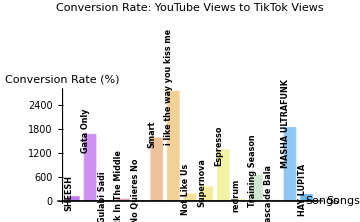
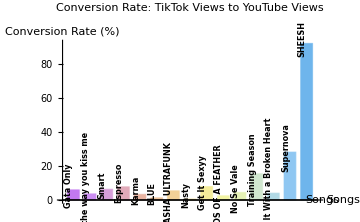
{Rank | Song Name | YouTube Views | TikTok Views | Conversion Rate (TikTok/YouTube)
1 | SHEESH | 359,896,095 | 390,081,328 | 108.40%
2 | Gata Only | 228,382,568 | 3,804,584,163 | 1666.00%
3 | Gulabi Sadi | 170,115,238 | 87,900 | 0.05%
4 | Stuck In The Middle | 147,951,356 | 70,103,300 | 47.38%
5 | Si No Quieres No | 135,893,150 | 147,200 | 0.11%
6 | Smart | 130,698,280 | 2,059,824,051 | 1576.00%
7 | i like the way you kiss me | 122,599,116 | 3,369,120,610 | 2748.00%
8 | Not Like Us | 116,347,040 | 208,339,025 | 179.10%
9 | Supernova | 111,310,770 | 393,973,528 | 353.90%
10 | Espresso | 107,550,212 | 1,379,499,000 | 1283.00%
11 | redrum | 105,148,629 | 43,993,800 | 41.84%
12 | Training Season | 66,691,067 | 431,390,500 | 646.80%
13 | Casca de Bala | 63,418,833 | 8,850,449 | 13.96%
14 | MASHA ULTRAFUNK | 57,665,106 | 1,059,880,600 | 1838.00%
15 | HAY LUPITA | 51,510,163 | 84,927,420 | 164.90%,-Graphics-,Rank | Song Name | TikTok Views | YouTube Views | Conversion Rate (YouTube/TikTok)
1 | Gata Only | 3,804,584,163 | 228,382,568 | 6.00%
2 | i like the way you kiss me | 3,369,120,610 | 122,599,116 | 3.64%
3 | Smart | 2,059,824,051 | 130,698,280 | 6.35%
4 | Espresso | 1,379,499,000 | 107,550,212 | 7.80%
5 | Karma | 1,314,113,353 | 43,892,777 | 3.34%
6 | BLUE | 1,225,345,800 | 16,038,053 | 1.31%
7 | MASHA ULTRAFUNK | 1,059,880,600 | 57,665,106 | 5.44%
8 | Nasty | 1,051,026,401 | 6,277,949 | 0.60%
9 | Get It Sexyy | 476,545,000 | 37,676,729 | 7.91%
10 | BIRDS OF A FEATHER | 443,104,700 | 11,033,725 | 2.49%
11 | No Se Vale | 441,343,495 | 19,658,783 | 4.45%
12 | Training Season | 431,390,500 | 66,691,067 | 15.46%
13 | I Can Do It With a Broken Heart | 411,722,900 | 16,747,466 | 4.07%
14 | Supernova | 393,973,528 | 111,310,770 | 28.25%
15 | SHEESH | 390,081,328 | 359,896,095 | 92.26%,-Graphics-}

```mathematica
youtubeToTiktokData=ReverseSortBy[Transpose[{varSong,varYoutubeViews,varTiktokViews}],#[[2]]&];
youtubeToTiktokTop15=Take[youtubeToTiktokData,15];

tiktokToYoutubeData=ReverseSortBy[Transpose[{varSong,varTiktokViews,varYoutubeViews}],#[[2]]&];
tiktokToYoutubeTop15=Take[tiktokToYoutubeData,15];

(*2. caculate conversin rate*)
youtubeToTiktokConversion=N[youtubeToTiktokTop15[[All,3]]/youtubeToTiktokTop15[[All,2]]]*100;

tiktokToYoutubeConversion=N[tiktokToYoutubeTop15[[All,3]]/tiktokToYoutubeTop15[[All,2]]]*100;

(*3. Organize table data*)
youtubeToTiktokTable=Map[{#[[1]],#[[2]],#[[3]],#[[4]]}&,Transpose[{youtubeToTiktokTop15[[All,1]],youtubeToTiktokTop15[[All,2]],youtubeToTiktokTop15[[All,3]],youtubeToTiktokConversion}]];

tiktokToYoutubeTable=Map[{#[[1]],#[[2]],#[[3]],#[[4]]}&,Transpose[{tiktokToYoutubeTop15[[All,1]],tiktokToYoutubeTop15[[All,2]],tiktokToYoutubeTop15[[All,3]],tiktokToYoutubeConversion}]];

(*4. set the table format*)
youtubeToTiktokGrid=Grid[Prepend[MapIndexed[{#2[[1]],#[[1]],Style[NumberForm[#[[2]],DigitBlock->3],Bold,14],Style[NumberForm[#[[3]],DigitBlock->3],Bold,14],Style[Row[{NumberForm[#[[4]],{4,2}],"%"}],Bold,14]}&,youtubeToTiktokTable],{"Rank","Song Name","YouTube Views","TikTok Views","Conversion Rate (TikTok/YouTube)"}],Frame->All,Spacings->{2,1},Background->{{LightGray,None},{None,LighterGray[0.9]}},Alignment->{{Center,Left,Center,Right,Right}},ItemSize->{{2,15,20,15,10}},LabelStyle->Directive[Bold,16]];

tiktokToYoutubeGrid=Grid[Prepend[MapIndexed[{#2[[1]],#[[1]],Style[NumberForm[#[[2]],DigitBlock->3],Bold,14],Style[NumberForm[#[[3]],DigitBlock->3],Bold,14],Style[Row[{NumberForm[#[[4]],{4,2}],"%"}],Bold,14]}&,tiktokToYoutubeTable],{"Rank","Song Name","TikTok Views","YouTube Views","Conversion Rate (YouTube/TikTok)"}],Frame->All,Spacings->{2,1},Background->{{LightGray,None},{None,LighterGray[0.9]}},Alignment->{{Center,Left,Center,Right,Right}},ItemSize->{{2,15,20,15,10}},LabelStyle->Directive[Bold,16]];

yTubeToTiktoksongNames={"SHEESH","Gata Only","Gulabi Sadi","Stuck In The Middle","Si No Quieres No","Smart","i like the way you kiss me","Not Like Us","Supernova","Espresso","redrum","Training Season","Casca de Bala","MASHA ULTRAFUNK","HAY LUPITA"};

tikToktoYTsongNames={"Gata Only","i like the way you kiss me","Smart","Espresso","Karma","BLUE","MASHA ULTRAFUNK","Nasty","Get It Sexyy","BIRDS OF A FEATHER","No Se Vale","Training Season","I Can Do It With a Broken Heart","Supernova","SHEESH"};

rotateLabels[labels_]:=Placed[Style[#,Italic,FontSize->8,Black]&/@labels,Above,Rotate[#,90 Degree]&];


(*5. set the graph format*)
youtubeToTiktokBarChart=BarChart[youtubeToTiktokConversion,ChartLabels->rotateLabels[yTubeToTiktoksongNames],ChartStyle->"Pastel",PlotLabel->"Conversion Rate: YouTube Views to TikTok Views",LabelStyle->Directive[Bold,Black,Smaller],AxesLabel->{"Songs","Conversion Rate (%)"},ImageSize->Medium,BarSpacing->0.4,ScalingFunctions->None];

tiktokToYoutubeBarChart=BarChart[tiktokToYoutubeConversion,ChartLabels->rotateLabels[tikToktoYTsongNames],ChartStyle->"Pastel",PlotLabel->"Conversion Rate: TikTok Views to YouTube Views",LabelStyle->Directive[Bold,Black,Smaller],AxesLabel->{"Songs","Conversion Rate (%)"},ImageSize->Medium,BarSpacing->0.4,ScalingFunctions->None];

(*6. outcome*)
{youtubeToTiktokGrid,youtubeToTiktokBarChart,tiktokToYoutubeGrid,tiktokToYoutubeBarChart}
```

### Insights and Cross - Platform Comparisons

#### (A) TikTok Views ↔ Spotify Streams Conversion Rate

1. Characteristics of High Conversion :
    - Songs like Beautiful Things and Magnetic achieved conversion rates of 168.30 % and 50.36 %, respectively, indicating that music clips that gained traction on TikTok successfully drove users to Spotify for full - length streaming .
      - TikTok' s viral mechanism works especially well for songs with distinct rhythms or catchy lyrics, effectively facilitating cross - platform conversion .
2. Reasons for Low Conversion :
      - Karma had a conversion rate of only 1.32 %, suggesting that although it attracted high TikTok views, the song failed to engage users on Spotify, likely due to its reliance on visual elements rather than strong musical appeal .
3. Insight :
    -TikTok' s short - video platform can amplify a song' s visibility, but only those that balance "clip appeal" and "overall musical quality" can achieve high conversion rates .

#### YouTube Views ↔ Spotify Streams Conversion Rate

1. Impact of Platform Characteristics :
  - High YouTube - view songs like SHEESH had a relatively low Spotify conversion rate of 34.70 %, highlighting its dependency on visuals rather than auditory engagement .
  - Conversely, songs like Gata Only and i like the way you kiss me achieved Spotify conversion rates of 295.60 % and 490.50 %, respectively, demonstrating their ability to thrive on both visual and audio - based platforms .
2. Challenges :
   -  Songs with high YouTube views but low Spotify streams reveal a lack of auditory appeal for purely listening - focused audiences .
3. Insight :
   -  YouTube leans toward visual and narrative - driven content, while Spotify emphasizes pure audio experiences . Songs need to balance "musicality" and "visual appeal" to succeed across both platforms .

#### YouTube Views ↔ TikTok Views Conversion Rate

1. High Conversion Rate Examples :
  - Songs like Gata Only and i like the way you kiss me achieved TikTok conversion rates of 1666.00 % and 1576.00 %, respectively, showcasing their exceptional viral potential on short - video platforms .
2. Challenges for Low Conversion :
   - HOLA PERDIDA had high YouTube views (143, 032, 680) but an extremely low TikTok conversion rate (0.00 %), indicating a lack of compatibility with TikTok' s short - video format or viral elements .
3. Insight :
   - YouTube' s long - form storytelling nature contrasts sharply with TikTok' s fragmented, bite - sized content . To achieve high TikTok conversion, songs must feature "short, distinct, and attention-grabbing moments.

#### Which Two Platforms Have the Most Efficient Conversion? Why?

Most Efficient Conversion : TikTok Views ↔ Spotify Streams
- Highest Average Conversion Rate : TikTok’ s viral short - video format provides an ideal foundation for generating user interest, while Spotify’ s full - song experience allows for further engagement .
 - Why? : TikTok grabs users’ attention through engaging clips, and Spotify provides a natural extension for users to enjoy the full song . Tracks like Beautiful Things and Magnetic leveraged TikTok’ s “clip appeal” to drive significant Spotify traffic .
 Second Most Efficient Conversion : YouTube Views ↔ Spotify Streams 
- Second - Highest Average Conversion Rate : YouTube’ s long - form videos build strong narratives, while Spotify offers a seamless listening experience . 
- Why? : Songs like Gata Only and i like the way you kiss me successfully leveraged YouTube’ s visual storytelling and Spotify’ s auditory appeal to achieve high conversion rates .

### Recommendations

Develop Strategies for TikTok and Spotify
1. Promote integrated content that combines short - form videos and music, leveraging TikTok trends to drive Spotify streams . For example, create curated Spotify playlists titled “TikTok Hits.”
2. Collaborate with TikTok influencers to guide users toward Spotify, utilizing the most engaging parts of songs to design challenges .

Enhance Collaboration Between YouTube and TikTok
1. Slice YouTube’s long-form video content into TikTok-friendly short clips, enabling a smoother flow of content between the two platforms.
2. Focus on YouTube Shorts as a bridge to amplify TikTok-viewed songs’ performance on YouTube.

Improve Low-Conversion Songs
1. Repackage content for low-conversion songs, testing newly designed video clips to increase appeal. For example, for Karma, introduce music-driven challenges or visually captivating elements.

Optimize Overall Brand Strategy
1. Build a “cross-platform music ecosystem,” promoting Spotify as the “final destination for music” while driving engagement from TikTok and YouTube.
2. Regularly update multi-platform collaborative “Top Songs” albums to sustain user interest.

Continuous Data Analysis and Experimentation
1. Continuously track cross-platform data and conduct A/B testing for different songs to determine which content formats drive the best multi-platform conversions.
2. Optimize conversion pathways between TikTok, YouTube, and Spotify, identifying the most effective promotion strategies.

## Genre and Top Artist Analysis

### Word Cloud

Stopwords[]

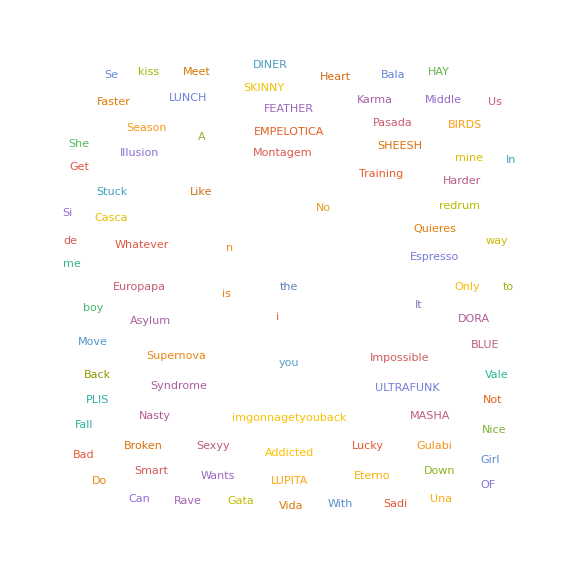

```mathematica
(*Step 2:Extract the second column*)tracks=varSong; (*Replace 2 with the correct column position if necessary*)

(*Step 3:Combine all track names into a single string*)
combinedText=StringJoin[Riffle[ToString/@tracks," "]];

(*Step 4:Tokenize words and remove stop words*)
words=TextWords[combinedText];

(*Step 5:Define a comprehensive stop word list*)
customStopWords=Stopwords[]

(*Filter out stop words*)
filteredWords=Select[words,!MemberQ[customStopWords,ToLowerCase[#]]&];

(*Step 6:Generate the word cloud*)
WordCloud[filteredWords,ImageSize->Large,Background->White]
```

Looking at the word cloud of track names from the 2024 dataset, several patterns emerge that hint at the popular genres and themes in music. Words like “Love,” “Heart,” “You,” “Me,” and “No” point toward themes of personal emotions, relationships, and romantic storytelling, which are central to genres like pop, R&B, and ballads. On the other hand, words like “Supernova,” “Training,” “Harder,” “Fall,” and “Asylum” suggest influences from more experimental, alternative, or even electronic and indie genres, which often explore abstract or intense themes. Additionally, terms like “Dance,” “Rave,” and “Sexy” reflect a continued popularity of high-energy dance tracks, often seen in EDM and Latin genres.

Recommendations:
1. Focus on Emotional Themes: Songs with relatable lyrics about love, heartbreak, or self-reflection continue to resonate with audiences. Pop and R&B tracks that explore these topics in a heartfelt way are likely to perform well.

2. Experiment with Edgy and Abstract Concepts: Words like “Supernova” and “Asylum” indicate a growing interest in creative, experimental music. Indie, alternative, and even cinematic electronic genres could tap into this trend, appealing to audiences looking for depth and uniqueness.

3. Emphasize Danceable Tracks: High-energy words like “Rave,” “Sexy,” and “Faster” show the enduring popularity of tracks meant for parties or clubs. Latin pop, EDM, and reggaeton tracks with infectious beats will attract listeners who enjoy moving to the music.

4. Incorporate Cross-Genre Appeal: Combining elements of emotional storytelling with energetic beats could create versatile tracks that work in multiple settings. For instance, a pop track with a danceable EDM remix can cater to both mainstream and club audiences.

5. Cultural Diversity: Words like “Bala,” “Lupita,” and “De” hint at international and bilingual influences. Songs that incorporate multicultural elements, languages, and rhythms (like Latin or Afrobeat) can attract global listeners.

By targeting these trends and blending emotional depth with dynamic rhythms, recording companies can craft songs that cater to a broad audience and stand out in the competitive music landscape of 2024.

### Top 5 Popular Artist Based On Average Spotify Streams

```mathematica
DynamicModule[{numArtists=5},Manipulate[Module[{artistStreams,groupedByArtist,averageStreamsByArtist,sortedArtists,selectedArtists,scaledStreams},(*Step 1:Combine Artist and Spotify Streams into a list of pairs*)
artistStreams=Transpose[{varArtist,varSpotifyStreams}];
(*Step 2:Group by artist and calculate average streams*)
groupedByArtist=GroupBy[artistStreams,First->Last];
averageStreamsByArtist=Association[KeyValueMap[#1->Mean[#2]&,groupedByArtist]];
(*Step 3:Sort artists by average streams in descending order*)
sortedArtists=ReverseSortBy[averageStreamsByArtist,#&];
(*Step 4:Select the top artists based on numArtists*)
selectedArtists=Take[sortedArtists,numArtists];
(*Step 5:Scale streams for readability (e.g.,divide by 1 million)*)
scaledStreams=N[Values[selectedArtists]]/10^6;
(*Step 6:Create a bar chart with custom colors and labels*)BarChart[scaledStreams,ChartLabels->Placed[Keys[selectedArtists],Top,Rotate[#,90 Degree]&],PlotLabel->"Top Artists by Average Spotify Streams (in millions)",ChartStyle->"Pastel",ImageSize->Large,BarSpacing->0.5]],{{numArtists,5,"Number of Top Artists"},1,Length[DeleteDuplicates[varArtist]],1}]]
```

This bar chart visualizes the top five artists by average Spotify streams (in millions). Here’s an interpretation and analysis:

Artists’ Rankings by Average Streams:
1. FloyyMenor leads with the highest average streams, approaching 700 million.
2. Artemas follows with an average slightly above 600 million streams.
3. Sabrina Carpenter takes third place, averaging around 550 million streams.
4. 21 Savage is fourth, with an average near 500 million streams.
5. Kendrick Lamar comes in fifth, with an average slightly above 400 million streams.


Value and Actionable Insights:
This graph provides valuable insights for song-making companies, especially in terms of strategic decision-making and market understanding. Here’s how this data can be leveraged:

1. Artist Selection for Collaborations
Value: Companies can identify which artists have high streaming averages (e.g., FloyyMenor and Artemas) and prioritize collaborations with them to maximize exposure and revenue.
Actionable Insight: Partner with these top performers for new projects, endorsements, or joint marketing campaigns to tap into their strong audience bases.

2. Understanding Market Trends
Value: The chart reflects what listeners are currently drawn to. If these artists represent specific genres or styles, it can guide companies to focus on producing similar types of music.
Actionable Insight: Research the genres or characteristics of the top-streamed artists’ music (e.g., beats, lyrics, mood) and incorporate them into future productions.

3. Promotion and Marketing Strategies
Value: The streaming numbers suggest potential return on investment for promotional campaigns. Companies can invest more in marketing the artists or genres that perform well.
Actionable Insight: Use this data to create targeted marketing campaigns that align with trends driven by these popular artists.

4. Talent Development
Value: Emerging or lesser-known artists can model their style and promotional strategies after those of the top performers.
Actionable Insight: Study the successful approaches of top artists (e.g., social media engagement, viral trends, collaborations) and apply these to develop rising stars.

5. Licensing and Distribution
Value: Companies can predict licensing demand for music used in films, TV, ads, or games based on these artists’ popularity.
Actionable Insight: Secure licensing deals for tracks from these artists, knowing their songs have proven mass appeal.

6. Global Expansion
Value: If the data reflects global trends, companies can focus on these artists for international markets. Conversely, if it’s regional data, this identifies untapped areas for growth.
Actionable Insight: Use top-performing artists to penetrate new geographical markets and tailor songs to those audiences.

7. Streaming Revenue Projections
Value: High average streams mean higher potential revenue. Knowing which artists consistently perform well allows better financial forecasting.
Actionable Insight: Focus resources on artists with strong track records of generating streams, which leads to increased streaming royalties.
This graph is essentially a roadmap for identifying lucrative opportunities and making data-driven decisions to stay competitive in the evolving music industry.

## Conclusion

As a business analyst at a record label, our goal is to develop the most effective promotional strategies by analyzing interaction patterns across platforms and song performance, ultimately enhancing the market impact of songs and increasing the commercial value of artists. In 2024, we found that YouTube, TikTok, and Spotify each have unique roles in driving traffic, fostering interaction, and promoting songs. Through data analysis, we can identify the characteristics and user behaviors of different platforms and design the most strategic marketing plans based on these insights.
 
Platform Value and Strategy

YouTube Insight: Use YouTube as a starting point to attract broad traffic, combining high-quality video storytelling to capture users’ attention. However, it is important to direct this traffic to high-engagement platforms like Spotify. 
TikTok Insight: TikTok users enjoy creating content, so partnering with TikTok influencers to design challenges can amplify a song’s popularity and attract a younger audience. 
Spotify Insight: Treat Spotify as the ultimate destination for song promotion, utilizing playlists for efficient distribution.

Cross-Platform Integration and Conversion Efficiency
 
TikTok to Spotify Insight: TikTok video content attracts user attention, and converting that attention to Spotify satisfies the demand for full-length songs. Cross-platform activities, such as linking TikTok challenges to Spotify playlists, can maximize conversion rates.
YouTube to Spotify Insight: Strengthen emotional storytelling and musical connection in videos to encourage users to transition from watching to deeper listening.

User Preferences and Market Trends 

Emotional Themes and High-Energy Music Insight: Emotional storytelling in music remains a mainstream theme. Combining emotional depth with energetic dance beats can create versatile songs for multiple settings, such as remixes of emotional pop songs with dance elements. 
Multicultural Market Opportunity Insight: Invest in creating music with international elements, particularly genres that incorporate diverse cultural features such as Latin or Afrobeat rhythms to attract global audiences.
Artist Collaboration and Strategy Insight: Artists with high average streaming numbers (e.g., FloyyMenor and Artemas) represent stable market appeal. Analyzing their success factors, such as music style and marketing strategies, can be applied to promoting emerging artists.

Actionable Recommendations

1) Invest in TikTok and Spotify collaboration activities to leverage viral content for full song plays.
2) Optimize YouTube content by combining narrative storytelling with the song’s unique characteristics to enhance cross-platform conversion.
3) Continuously track data and adjust strategies for low-conversion songs, such as redesigning visual content or rebranding the songs.
4) Develop multicultural music production and use it as a core strategy for expanding into global markets.

In conclusion, our analysis not only highlights the complementary roles of each platform but also emphasizes how to maximize conversion rates across platforms and enhance the global influence of artists. With a deep understanding of these platforms, record labels can tailor promotional strategies for each song, helping them stand out in the competitive music market. We will continue to track data and adjust strategies based on market trends, ensuring that we remain at the forefront of the evolving music industry.

## Works Cited

Data source: 
Elgiriyewithana, N. (2024) Most streamed Spotify Songs 2024, Kaggle. Available at: https://www.kaggle.com/datasets/nelgiriyewithana/most-streamed-spotify-songs-2024 (Accessed: 08 December 2024). 
Image source: Apple Music, Spotify, YouTube Music, Soundcloud - a set of logos for popular music streaming services. logos on transparent background for your design. PNG Image Stock Photo (no date) Adobe Stock. Available at: https://stock.adobe.com/images/apple-music-spotify-youtube-music-soundcloud-a-set-of-logos-for-popular-music-streaming-services-logos-on-transparent-background-for-your-design-png-image/538862071?asset_id=538862071 (Accessed: 08 December 2024).